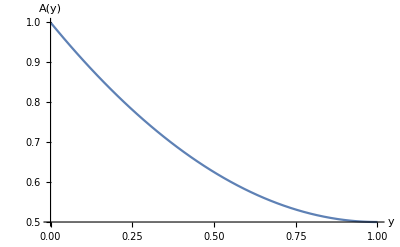

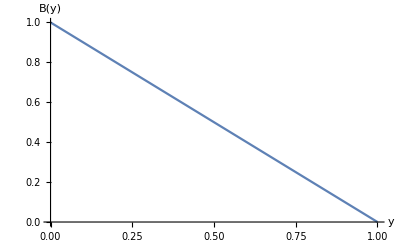

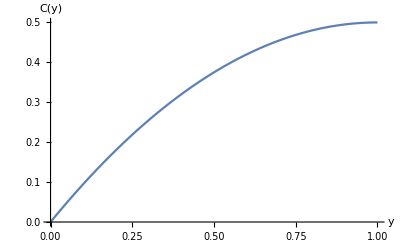

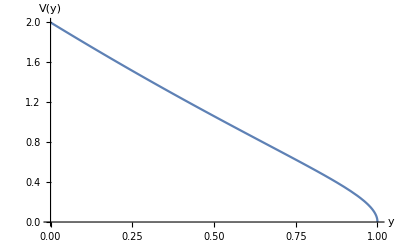

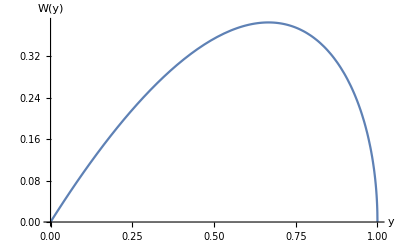

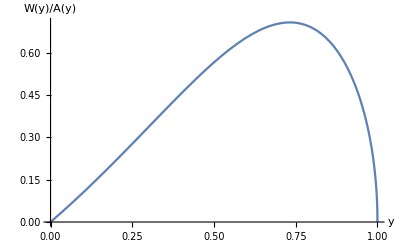

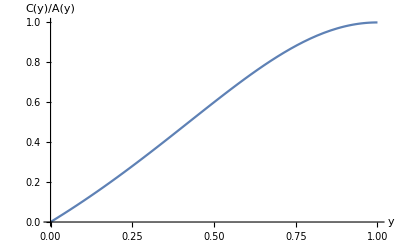

```mathematica
a[y_]=1-y+y*y/2;
b[y_]=1-y;
c[y_]=y*(1-y/2);
v[y_]=(2-y)*Sqrt[1-y];
w[y_]=y*Sqrt[1-y];
Plot[a[y],{y,0,1},AxesLabel->{"y","A(y)"}]
Plot[b[y],{y,0,1},AxesLabel->{"y","B(y)"}]
Plot[c[y],{y,0,1},AxesLabel->{"y","C(y)"}]
Plot[v[y],{y,0,1},AxesLabel->{"y","V(y)"}]
Plot[w[y],{y,0,1},AxesLabel->{"y","W(y)"}]
Plot[w[y]/a[y],{y,0,1},AxesLabel->{"y","W(y)/A(y)"}]
Plot[c[y]/a[y],{y,0,1},AxesLabel->{"y","C(y)/A(y)"}]
```

(4-4 y)/(2+(-2+y) y)^2

(4-6 y+y^3)/(√(1-y) (2+(-2+y) y)^2)

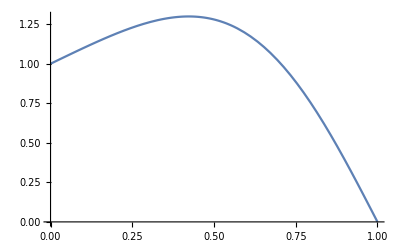

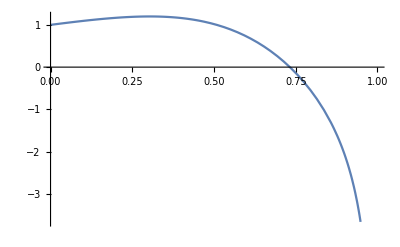

0.829877

```mathematica
dca[y_]=FullSimplify[D[c[y]/a[y],y]]
dwa[y_]=FullSimplify[D[w[y]/a[y],y]]
Plot[dca[y],{y,0,1}]
Plot[dwa[y],{y,0,1}]
N[dca[0.77]]
```

```mathematica
N[dca[0.64]]
N[dwa[0.64]]
```

1.12853

0.551391